```mathematica
A=1;
theta=2*Pi/24;
w=0;
degradation=1;
x0=0;
discontinuity[x_,t_]:=If[t<12,x,x^2/11];
s=NDSolve[{x'[t]==A*(1+Cos[theta*t-w])-degradation*x[t]+discontinuity[x[t],t],x[0]==x0},x,{t,0,24}];
Plot[Evaluate[x[t]/. s],{t,0,24},PlotRange->All]
```

NDSolve::ndsz: At t == 14.4738, step size is effectively zero; singularity or stiff system suspected.

-Graphics-

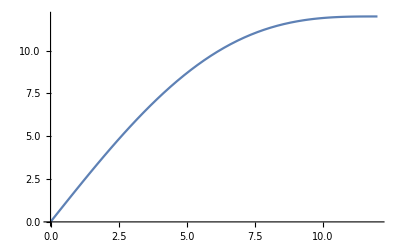

```mathematica
Plot[Evaluate[x[t]/. s],{t,0,12},PlotRange->All]
```

```mathematica
Plot[Evaluate[x[t]/. s],{t,12,24},PlotRange->All]
```

-Graphics-